# Cribbage

## Card Utilities

Cards are represented as numbers from 1-52 which is also the convention used by the PlayingCardGraphic resource.  We need to access the suit of a card which is 1 + Floor[(n - 1)/13] and the rank which is 1 + Mod[n - 1, 13].  We also need to know the value of a card which in Cribbage is the number for Ace through Ten and 10 for Jack, Queen, King in other words Min[rank[n], 10].

```mathematica
suit[n_Integer] := 1 + Floor[(n - 1)/13]
rank[n_Integer] := 1 + Mod[n - 1, 13]
```

The following are convenience methods for display which map suit and rank numbers to their standard names.

```mathematica
cardLetters = {"A", "2", "3", "4", "5", "6", "7", "8", "9", "10", "J", "Q", "K"};

displayCard[n_Integer] := ResourceFunction["PlayingCardGraphic"][{n}, "CardSpreadAngle" -> 0, "ImageSize" -> Small]
displayCards[h_List] := ResourceFunction["PlayingCardGraphic"][h, "CardSpreadAngle" -> 0, "ImageSize" -> Small, "CardOffset" -> {0.5, 0}]

suitNames = {"Spades", "Hearts", "Diamonds", "Clubs"};
suitLetters = StringPart[#, 1]& /@ suitNames;

cardNames = Table[cardLetters[[rank[i]]] <> suitLetters[[suit[i]]], {i, 52}];
card[name_String] := Position[cardNames, name][[1]][[1]]
```

```mathematica
Options[ResourceFunction["PlayingCardGraphic"]]
```

{CardSpreadAngle→π/4,CardOffset→{0.3,0},CardColor→GrayLevel[1],CardReverse→Automatic,FontColor→Automatic,FontFamily→Arial,FontSize→Scaled[0.15],RoundingRadius→0.07,AlignmentPoint→Center,AspectRatio→Automatic,Axes→False,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelStyle→{},Method→Automatic,PlotLabel→None,PlotRange→All,PlotRangeClipping→False,PlotRangePadding→Automatic,PlotRegion→Automatic,PreserveImageOptions→Automatic,Prolog→{},RotateLabel→True,Ticks→Automatic,TicksStyle→{}}

```mathematica
Head[displayCard[1]]
```

Graphics

```mathematica
Attributes[Graphics]
```

{Protected,ReadProtected}

## Counting

There are two types of scoring in Cribbage, counting and pegging.  We will deal with them in the reverse order in which they appear during the game.   At the end of the hand there will be three sets of cards corresponding to the pone’s hand, the dealer’s hand and the crib scored in that order.  The order is important since the game is won by the first player to hit a score of 121 at which point all scoring stops.

There is a starter card or cut card displayed at the beginning of the hand which is used by all three hands and known to all players, therefore the scoring will take two arguments, the starter card and the four hand cards.  There is one special rule unique to scoring the crib we will describe later.

There are six components to computing the final count:

- nob (colloquially “one for his nob”) is a single point given to a  hand containing a Jack of the same suit as the starter card
By subtracting the rank of the start card from its value from its number we get the zeroth element of that suit and adding 11 gives the Jack of the same suit

```mathematica
nob[s_, h_] := If[MemberQ[h, 11 + s - rank[s]], 1, 0]
```

- flush - if all the four hand cards and the starter card have the same suit, score 4.  If the four hand cards have the same suit but the starter card has a different suit, score 4 but only if scoring a player hand and not the crib.

For the moment we code this as two functions instead of adding a flag.

```mathematica
flush[s_, h_] := If[CountDistinct[suit /@ h] == 1, If[suit[s] == suit[h[[1]]], 5, 4], 0]
cribFlush[s_, h_] := If[CountDistinct[suit /@ Append[h, s]] == 1, 5, 0]
```

- pairs - Note that from now on all further scoring depends solely on the rand and not the suit of the cards.  Score 2 points for every pair.  In the case of a triplet one scores 6 for the three possible pairs (this is known as a pair royal) and four-of-a-kind scores 12 (double pair royal).

Conveniently the score for a triple or four of a kind is arranged to be exactly what one gets by counting only pairs.  This is also the first of the scoring categories making no distinction between the starter card and the rest of the hand.

```mathematica
pairs[h_] := 2 * Length[Select[Subsets[rank /@ h, {2}],
				 (#[[1]] == #[[2]])&]]
pairs[s_, h_] := pairs[Append[h, s]]
```

- sequences - three or more consecutive cards score the length of the sequence.

Unlike pairs, a naive sum over subsets would over count.  E.g, four in a sequence includes two subsequences of length three which would return six instead of four.  A similar situation happens with five.  We therefore use a correction factor depending on the sequence length.

```mathematica
seqScore[s_] := If[Sort[s] == Range[Min[s], Max[s]], <|3->3, 4->-2, 5->0|>[Length[s]], 0]

sequences[s_] := Plus @@ seqScore /@ Subsets[rank /@ s, {3, 5}]
sequences[s_, h_] := sequences[Append[h, s]]
```

- fifteens - score two points for every combination of two or more cards totaling 15 points.  Note that a given card can be involved in multiple combinations, so, for example, 5, 5, Q, J would yield 8 points for combinations of each 5 with each face card.

```mathematica
fifteens[h_] := 2 * Length[Position[Plus @@@ Subsets[value /@ h, {2, 5}], 15]]
fifteens[s_, h_] := fifteens[Append[h, s]]
```

The final count is simply the sum of the functions above.

```mathematica
count[s_, h_] := nob[s, h] + flush[s,h] + pairs[s,h] + sequences[s,h] + fifteens[s,h]
countCrib[s_, h_] := nob[s, h] + cribFlush[s,h] + pairs[s,h] + sequences[s,h] + fifteens[s,h]
```

## Underlying Utilities

The  following utilities are used in determining which cards can be legally played to a sequence.

```mathematica
value[0] = 0;
value[card_Integer] := Min[rank[card], 10]
```

```mathematica
addValue[acc_Integer, card_Integer] := If[value[card] == 0, 0, acc + value[card]]
sequenceValue[sequence_List] := Fold[addValue, 0, sequence]
```

## Play of the Hand

Cribbage is played over a series of hands until one player has achieved 121 points.  Hands are represented as: 
	{{player 1 hand}, {player 2 hand}, start card}
Note that at the start of the hand each player has six cards in their hand and no discards and the start card is not yet known to the players.

```mathematica
dealHand[] := With[{dealt = RandomSample[Range[52], 13]}, {dealt[[1;;6]], dealt[[7;;12]], dealt[[13]]}]
```

A new game consists of the scores {player1, player2}, the hand number and the cards comprising the first hand.  An odd hand number indicates that player1 is the dealer and an odd hand number represents a hand dealt by player2.  There are also (initially empty) lists which will hold player discards that will eventually form the crib and the sequence of cards played.  This data structure forms a “game state” and the game will be processed as a series of game states.  Expanded:

### Game State

{{player 1 score, player 2 score}, hand number, {player 1 hand}, {player 2 hand}, {start card}, {player 1 discards}, {player 2 discards}, {sequence}}

Note that during the discard phase, two cards will be moved from the players’ hands to their respective discards and during the play of the hand the sequence of cards played will duplicate cards in the players’ hands as there would otherwise not be a way to distinguish which player played which card.

```mathematica
newGame[] := Join[{{0,0}, 1}, dealHand[], {{}, {}, {}}]
```

Each player only has access to a subset of the game data.  Both players know the current score, their own initial hand and discards, and any cards played to the sequence independent of who played them.  Also, once the initial discard has completed (i.e., the number of cards in ones hand are four instead of six), the player can see the value of the start card.

The input to this function is a gameState which contains information about both players and what is returned is a playerState which is specific to one of the two players.  The output is a playerState comprising:

```mathematica
displayGameState[gs_] := Grid[{{Text[Style[gs[[1]], FontSize -> 36]],Text[Style[gs[[2]], FontSize -> 36]], displayCard[gs[[5]]]}, {displayCards[gs[[3]]], displayCards[gs[[6]]]},
 {displayCards[gs[[4]]], displayCards[gs[[7]]]}, {displayCards[gs[[8]]]}}]
```

### Player State

{player number, {score}, hand number, {player hand}, {start card}, {player discards}, {sequence}}
Note that the start card will be visible if and only if the discards list is non-empty (which in turn is if and only if the number of cards the in the player’s hand is 4 instead of 6), otherwise they see the placeholder value of 0.

```mathematica
playerState[player_Integer, gs_List] := Join[
{player},
Take[gs, 2],
{gs[[2 + player]]},
If[Length[gs[[2 + player]]] == 4,
{gs[[5]], gs[[5 + player]]},
{0, {}}],
{Last[gs]}
] /; 1 <= player <= 2 && Length[gs] == 8
```

```mathematica
playerState[1, newGame[]]
```

In the discard phase, the player can choose any two of the six cards leading to fifteen possibilities.  Since this decision is made by a player based on their available information, the input is a playerState and the output is a list of possible successor playerStates.

```mathematica
potentialDiscards[ps_List] := Table[
Join[
Take[ps, 3], 
{Complement[ps[[4]], d]},
 {{}}, {d}, {{}}],
{d, Subsets[ps[[4]], {2}]}] /; Length[ps] == 7 && Length[ps[[4]]] == 6
```

If the discard phase is over, i.e., the game state has two hands of four cards and each player has two discards, the next player to pay is either the player who is not the dealer if the sequence of cards played is empty and otherwise is the player who did not play the last card to the sequence (ignoring 0 which represents a “go”)

```mathematica
nextToPlay[gs_] := If[OddQ[gs[[2]]], 2, 1] /; Length[gs[[3]]] == 4 && Length[gs[[8]]] == 0 && (Count[gs[[8]], x_?Positive] < 8)
nextToPlay[gs_] := If[MemberQ[gs[[3]], Last[Select[gs[[8]], Positive]]], 2, 1] /; Length[gs[[3]]] == 4 && (Count[gs[[8]], x_?Positive] < 8)
```

## Pegging

After the discards there are potential cards played to the sequence.  The legal cards are those which do not increase the sequence value over 31 (a 0 represents a “go” resetting the count to 0).

```mathematica
filterLegal[hand_, sequence_] := Select[hand, (FreeQ[sequence, #]  && (value[#] + sequenceValue[sequence] <= 31))&]
```

In case neither player has a legal play, we append a 0 (“go”) to the sequence and credit the last person to play with two points if the current sequence total is 31 and one point otherwise.

```mathematica
mustSayGo[gs_] := Length[filterLegal[Join[gs[[3]], gs[[4]]], gs[[8]]]] == 0
```

```mathematica
potentialPlays[ps_list] := Table[
Append[Most[ps], Append[Last[ps], legal]], 
{legal, Select[(value[#] + sequenceValue[Last[ps]] <= 31)&, ps[[3]]]}]/; Length[ps] == 7
```

```mathematica
goScore[score_, lastPlayer_, thirtyOne_] := If[lastPlayer == 1,{Min[121, score[[1]] + If[thirtyOne, 2, 1]], score[[2]]}, {score[[1]], Min[121, score[[2]] + If[thirtyOne, 2, 1]]}]
```

## Accept Discards

Merge in the players’ decisions on which cards to discard.  Since this is also the point at which the start card becomes visible, this is also when two points are awarded to the dealer if the start card happens to be a Jack (“two for his heels”).

```mathematica
acceptDiscards[gs_List, p1State_List, p2State_List] :=
{
If[rank[gs[[5]][[1]]] == 11,(* start card is a Jack; dealer scores two for his heels *)
If[OddQ[gs[[2]]],
{Min[121, gs[[1]][[1]] + 2], gs[[1]][[2]]},
{gs[[1]][[1]], Min[121, gs[[1]][[2]] + 2]}],
gs[[1]]],
gs[[2]],(* hand number *)
p1State[[4]], p2State[[4]], (* hands *)
gs[[5]],(* start card *)
p1State[[6]], p2State[[6]] ,(* discards *)
{} (* sequence which is always empty at this point in the game *)
}
```

## New Hand

After the hand has been played out (sequence is of length eight excluding 0’s), the hands are scored with the non-dealer’s (pone’s) score computer first and then the dealer is given points for their hand and the crib.  If the initial computation pushes the pone’s score to 121, the game is over and the dealer’s score is never calculated.

```mathematica
newHand[gs_List] := Module[{p1Score=gs[[1]][[1]], p2Score =gs[[1]][[2]],handNumber=gs[[2]], p1Hand=gs[[3]], p2Hand=gs[[4]], start=gs[[5]], p1Discards=gs[[6]], p2Discards=gs[[7]],p1HandCount, p2HandCount, cribCount},
p1HandCount = count[start, p1Hand];
p2HandCount = count[start, p2Hand];
cribCount = countCrib[start, Join[p1Discards, p2Discards]];
If[OddQ[handNumber],
(* p1 is dealer *)
p2Score = Min[121, p2Score + p2HandCount];
If [p2Score < 121,
p1Score = Min[121, p1Score + p1HandCount + cribCount]],
(* p2 is dealer *)
p1Score = Min[121, p1Score + p1HandCount];
If [p1Score < 121,
p2Score = Min[121, p2Score + p2HandCount + cribCount]]];
Join[{{p1Score, p2Score}, handNumber + 1}, dealHand[], {{}, {}, {}}]]
```

## Next State

The nextState function represents the core functionality of the cribbage game.  The input is a 4-tuple (in the initial call choices is an empty list and therefore can be omitted)

```mathematica
nextState[{p1_, p2_, gs_}] := nextState[{p1, p2, gs, {}}]
```

If you have reached 121 points, return the input

The game is over when one player reaches 121 points in which case the nextState function reaches a fixed point.

```mathematica
nextState[{p1_, p2_, gs_, choices_}] := {p1, p2, gs, choices} /; Max[gs[[1]]] == 121
```

The next state function depends on what decisions come next.  If there are six cards in each player’s hand, the next action is selection by each player of two cards to discard to form the crib.  Generally no scoring takes place at this point, except in the case in which the start card (which the players do not know until after the discard) is a Jack in which case the dealer scores two points “for his heels”, and in rare cases this could trigger the end of the game.

```mathematica
nextState[{p1_, p2_, gs_, choices_}] := With[{d1 = p1[potentialDiscards[playerState[1, gs]]], d2 = p2[potentialDiscards[playerState[2, gs]]]},
{p1, p2, acceptDiscards[g, d1, d2], Join[choices,{d1, d2}]}] /; Length[gs[[3]]] == 6
```

The last element in the game state represents the cards played by the players and if the sequence has length eight (and the last entry is a 0 indicating that the “go” has been scored) , all the cards have been played and the next hand begins.  It is at this point that hands are scored in the order the pone (non-dealer’s) hand, the dealer’s hand and the crib (whose points also are attributed to the dealer).  The order is important because if the scoring of the pone’s hand causes that player’s total to equal 121, the game ends immediately.

```mathematica
nextState[{p1_, p2_, gs_, choices_}] := {p1, p2, newHand[gs], choices} /; (Count[gs[[8]], x_?Positive] == 8) && (Last[gs[[8]]] == 0)
```

The final possibility is that the current state requires one or the other player to play a card.  For the potential pegging plays, if the nextToPlay player has legal plays, the next move is chosen from that list, else if the opponent of that player can play, the next move is chosen from legal plays for that player.  If neither player has a legal play, a zero is added to the sequence and if the current total is 31 the last person to play gets 2 points otherwise they get 1.

```mathematica
nextState[{p1_, p2_, gs_, choices_}] := With[ {lastPlayer = If[MemberQ[gs[[3]],Last[gs[[8]]]], 1, 2], thirtyOne = sequenceValue[gs[[8]]] == 31},
{p1, p2, {goScore[gs[[1]], lastPlayer, thirtyOne], gs[[2]], gs[[3]], gs[[4]], gs[[5]], gs[[6]], gs[[7]], Append[gs[[8]], 0]}, choices} /; mustSayGo[gs]
```

Else one or other player chooses a card to play to the sequence.

```mathematica
(* nextState[{p1_, p2_, gs_, choices_}] := With[{d1 = p1[potentialPlays[playerState[1, gs]]], d2 = p2[potentialPlays[playerState[2, gs]]]},
{p1, p2, acceptPlays[gs, d1, d2], Join[choices,{d1, d2}]}] *)
```

## Scratch

{{player 1 score, player 2 score}, hand number, {player 1 hand}, {player 2 hand}, {start card},  {player 1 discards}, {player 2 discards}, {sequence}}

```mathematica
newHand[gs_List] := With[{p1Score=gs[[1]][[1]], p2Score =gs[[1]][[2]],handNumber=gs[[2]], p1Hand=gs[[3]], p2Hand=gs[[4]], start=gs[[5]], p1Discards=g1[[6]], p2Discards=gs[[7]], p1HandCount, p2HandCount, cribCount},
p1HandCount = count[start, p1Hand];
p2HandCount = count[start, p2Hand];
cribCount = countCrib[start, Join[p1Discards, p2Discards]];
If[OddQ[handNumber],
(* p1 is dealer *)
p2Score = Min[121, score[[2]] + p2HandCount];
If [p2Score < 121,
p1Score = Min[121, score[[1]] + p1HandCount + cribCount]],
(* p2 is dealer *)
p1Score = Min[121, score[[1]] + p1HandCount];
If [p1Score < 121,
p2Score = Min[121, score[[2]] + p2HandCount + cribCount]]];
Join[{{p1Score, p2Score}, handNumber + 1}, dealHand[], {{}, {}, {}}]]
```

```mathematica
g = newGame[]
```

```mathematica
d1 = RandomChoice[potentialDiscards[playerState[1, g]]]
```

```mathematica
d2 = RandomChoice[potentialDiscards[playerState[2, g]]]
```

```mathematica
g2 = acceptDiscards[g, d1, d2]
```

```mathematica
Length[g]
```

```mathematica
Length[g2]
```

```mathematica
g2[[1]]
```

```mathematica
Transpose[{g, g2}] // Grid
```

```mathematica
f[x_] := x^2
```

```mathematica
Head[f]
```

```mathematica
nextState[{p1_, p2_, gs_, choices_}] := With[{d1 = p1[potentialDiscards[playerState[1, gs]]], d2 = p2[potentialDiscards[playerState[2, gs]]]},
{p1, p2, acceptDiscards[g, d1, d2], Join[choices,{d1, d2}]}] /; Length[gs[[3]]] == 6
```

```mathematica
nextState[nextState[{RandomChoice, RandomChoice, g}]]
```

```mathematica
Clear[nextState]
```

```mathematica
g
```

```mathematica
Max[g[[1]]]
```

```mathematica
nextState[{p1_, p2_, gs_}] := nextState[{p1, p2, gs, {}}]
```

```mathematica
nextState[{p1_, p2_, gs_, choices_}] := {p1, p2, gs, choices} /; Max[gs[[1]]] == 121
```

```mathematica
Clear[nextState]
```

```mathematica
Length[g]
```

```mathematica
g[[8]]
```

```mathematica
nextState[{p1_, p2_, gs_, choices_}] := {p1, p2, newHand[gs], choices} /; Length[gs[[8]] == 8]
```

```mathematica
g
```

```mathematica
gh = {{0,0},1,{7,31,11,25},{24,45,10,48},{15},{47, 3},{4, 27},{7, 31, 11, 25, 24, 45, 10, 48}}
```

```mathematica
nextState[{RandomChoice, RandomChoice, gh, {}}]
```

```mathematica
Length[gh[[8]]]
```

```mathematica
?nextState
```

```mathematica
gh
```

```mathematica
gh = {{0,0},1,{7,31,11,25},{24,45,10,48},15,{47,3},{4,27},{7,31,11,25,24,45,10,48}}
```

{{0,0},1,{7,31,11,25},{24,45,10,48},15,{47,3},{4,27},{7,31,11,25,24,45,10,48}}

```mathematica
{{0,0},1,{7,31,11,25},{24,45,10,48},15,{47,3},{4,27},{7,31,11,25,24,45,10,48}}
```

```mathematica
newHand[gh]
```

```mathematica
dealHand[]
```

```mathematica
{{3,32,41,47,34,45},{38,11,48,51,4,19},16}
```

```mathematica
p1HandCount = count[gh[[5]], gh[[4]]]
```

```mathematica
count[16, {3,32,41,47}]
```

```mathematica
Length[gh[[8]]]
```

```mathematica
newHand[gh]
```

```mathematica
gh
```

```mathematica
sequenceValue[{7,31,11,0, 25,24,45,0, 10,48}]
```

```mathematica
displayCards[{7,31,11,25,24,45,10,48}]
```

```mathematica
gh
```

```mathematica
{{0,0},1,{7,31,11,25},{24,45,10,48},15,{47,3},{4,27},{7,31,11,25,24,45,10,48}}
```

```mathematica
gh = {{0,0},1,{7,31,11,25},{24,45,10,48},15,{47,3},{4,27}, {}}
```

```mathematica
Flatten[gh]
```

```mathematica
rank[0]
```

```mathematica
Table[value[c], {c, 0, 26}]
```

```mathematica
Count[{0, 1, 2, 3, 4}, x_?Positive]
```

```mathematica
filterLegal[hand_, sequence_] := Select[hand, (FreeQ[sequence, #]  && (value[#] + sequenceValue[sequence] <= 31))&]
```

```mathematica
s = {7,31,11}
```

```mathematica
h = {20, 45,10,48}
```

```mathematica
filterLegal[h, s]
```

```mathematica
Select[{0, 1, 2, 3, 0}, Positive]
```

{1,2,3}

```mathematica
MemberQ[{1, 2, 3}, 4]
```

False

```mathematica
gh = {{0,0},1,{7,31,11,25},{24,45,10,48},15,{47,3},{4,27},{24,31,11,25,24,45,7}}
```

{{0,0},1,{7,31,11,25},{24,45,10,48},15,{47,3},{4,27},{24,31,11,25,24,45,7}}

```mathematica
{{0,0},1,{7,31,11,25},{24,45,10,48},15,{47,3},{4,27},{24,31,25,24,45,7, 0}}
```

{{0,0},1,{7,31,11,25},{24,45,10,48},15,{47,3},{4,27},{24,31,25,24,45,7,0}}

```mathematica
nextToPlay[gh]
```

2

```mathematica
Clear[nextToPlay]
```

```mathematica
display[gs_] := Grid[{{Text[Style[gs[[1]], FontSize -> 36]],Text[Style[gs[[2]], FontSize -> 36]], displayCard[gs[[5]]]}, {displayCards[gs[[3]]], displayCards[gs[[6]]]},
 {displayCards[gs[[4]]], displayCards[gs[[7]]]}, {displayCards[gs[[8]]]}}]
```

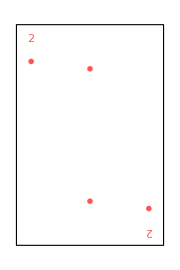
{0,0} | 1 | -Graphics-
-Graphics- | -Graphics- | 
-Graphics- | -Graphics- | 
-Graphics- |  |

```mathematica
display[gh]
```